```mathematica
quit;
Clear[o,r,c,s,x,AR,sig0,l1,l2,ss,entro,si1,si2,si3,si11,si12,si13,si21,si22,si23,si31,si32,si33,sig11,sig12,sig13,sig21,sig22,sig23,sig31,sig32,sig33]; 
sig0 = ({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});
l2[o_,r_] := E^(o √(1-1/r));
l1[o_,r_] := 1/l2[o,r];
entro[x_]:= -x Log[2,x];
ss[p1_,p2_,p3_,p4_] := -p1 Log[2,p1]-p2 Log[2,p2]-p3 Log[2,p3]-p4 Log[2,p4];

c[o_,r_]:= 1/(√(1+l1[o,r]));
s[o_,r_]:= √(1-c[o,r]^2);
AR[o_,r_] := 1/3({{c[o,r]^4, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, c[o,r]^2+c[o,r]^2 s[o,r]^2, 0, 0, c[o,r]^3, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, c[o,r]^2 s[o,r]^2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, s[o,r]^2+s[o,r]^4, 0, 0, c[o,r] s[o,r]^2, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, c[o,r]^3, 0, 0, c[o,r]^4, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, c[o,r]^2 s[o,r]^2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, c[o,r] s[o,r]^2, 0, 0, c[o,r]^2 s[o,r]^2, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, s[o,r]^4, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}}) 
si1=1/2({{0, √3, 0, 0}, {√3, 0, 2, 0}, {0, 2, 0, √3}, {0, 0, √3, 0}});
si2=1/2({{0, -I √3, 0, 0}, {I √3, 0, -2I, 0}, {0, 2I, 0, -I √3}, {0, 0, I √3, 0}});
si3=1/2({{3, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -3}});
si11=KroneckerProduct[Eigenvectors[si1][[1]],Eigenvectors[si1][[1]]*];
si12=KroneckerProduct[Eigenvectors[si1][[2]],Eigenvectors[si1][[2]]*];
si13=KroneckerProduct[Eigenvectors[si1][[3]],Eigenvectors[si1][[3]]*];
si14=KroneckerProduct[Eigenvectors[si1][[4]],Eigenvectors[si1][[4]]*];
si21=KroneckerProduct[Eigenvectors[si2][[1]],Eigenvectors[si2][[1]]*];
si22=KroneckerProduct[Eigenvectors[si2][[2]],Eigenvectors[si2][[2]]*];
si23=KroneckerProduct[Eigenvectors[si2][[3]],Eigenvectors[si2][[3]]*];
si24=KroneckerProduct[Eigenvectors[si2][[4]],Eigenvectors[si2][[4]]*];
si31=KroneckerProduct[Eigenvectors[si3][[1]],Eigenvectors[si3][[1]]*];
si32=KroneckerProduct[Eigenvectors[si3][[2]],Eigenvectors[si3][[2]]*];
si33=KroneckerProduct[Eigenvectors[si3][[3]],Eigenvectors[si3][[3]]*];
si34=KroneckerProduct[Eigenvectors[si3][[4]],Eigenvectors[si3][[4]]*];
sig11=si11/Tr[si11];
sig12=si12/Tr[si12];
sig13=si13/Tr[si13];
sig14=si14/Tr[si14];
sig21=si21/Tr[si21];
sig22=si22/Tr[si22];
sig23=si23/Tr[si23];
sig24=si24/Tr[si24];
sig31=si31/Tr[si31];
sig32=si32/Tr[si32];
sig33=si33/Tr[si33];
sig34=si34/Tr[si34];
```

```mathematica
(Eigenvectors[si1][[1]].Eigenvectors[si2][[4]])^2
N[Log[2,8/3]]
```

8 ⅈ

1.41504

```mathematica
(*--------------------------------AR----------------------------------*)
Clear[eigAR,sAR];
eigAR[o_,r_]=Simplify[Eigenvalues[AR[o,r]]];
sAR[o_,r_] = Simplify[ss[eigAR[o,r][[9]],eigAR[o,r][[10]],eigAR[o,r][[11]],eigAR[o,r][[12]]]+ss[eigAR[o,r][[13]],eigAR[o,r][[14]],eigAR[o,r][[15]],eigAR[o,r][[16]]]];
N[sAR[50,1]]
N[sAR[50,1.05]]
```

2.48802

0.918773

```mathematica
(*--------------------------------A----------------------------------*)
Clear[A,pA,sA,r];
A[o_,r_] = Simplify[Map[Tr,Partition[AR[o,r],{4,4}],{2}]];
pA[o_,r_] = Simplify[Tr[A[o,r]]]
A[o_,r_] = Simplify[A[o,r]/pA[o,r]];
sA[o_,r_] = Simplify[ss[A[o,r][[1,1]],A[o,r][[2,2]],1,1]];
N[sA[50,1.00]]
N[sA[50,1.05]]
```

1

0.918296

0.918296

```mathematica
(*--------------------------------R----------------------------------*)
Clear[R,pR,sR,r];
R[o_,r_] = AR[o,r][[1;;4,1;;4]]+AR[o,r][[5;;8,5;;8]]+AR[o,r][[9;;12,9;;12]]+AR[o,r][[13;;16,13;;16]];
pR[o_,r_] = Simplify[Tr[R[o,r]]];
R[o_,r_] = Simplify[R[o,r]/pR[o,r]];
sR [o_,r_] = Simplify[ss[R[o,r][[1,1]],R[o,r][[2,2]],R[o,r][[3,3]],R[o,r][[4,4]]]];
sR[50,1.00]
N[sR[50,1.05]]
```

1.9183

0.918622

```mathematica
(*--------------------------------X----------------------------------*)
```

```mathematica
(*---------------S(Subscript[ρ, 0]^x)-------------------*)
Clear[X0,pX0,sX0];
X0[o_,r_] := KroneckerProduct[sig11,sig0].AR[o,r];
X0[o_,r_]= X0[o,r][[1;;4,1;;4]]+X0[o,r][[5;;8,5;;8]]+X0[o,r][[9;;12,9;;12]]+X0[o,r][[13;16,13;;16]];
pX0[o_,r_] = Simplify[Tr[X0[o,r]]]
X0[o_,r_] = Simplify[X0[o,r]/pX0[o,r]];
X0[o_,r_] = Simplify[Eigenvalues[X0[o,r]]];
sX0 [o_,r_] = Simplify[ss[X0[o,r][[1]],X0[o,r][[2]],X0[o,r][[3]],X0[o,r][[4]]]];
N[sX0[50,1]]
N[sX0[50,1.05]]
```

5/24

1.78735

0.250593

```mathematica
(*---------------Subscript[ρ, 1]^x-------------------*)
Clear[X1,pX1,X1,sX1];
X1[o_,r_] := KroneckerProduct[sig12,sig0].AR[o,r];
X1[o_,r_] = X1[o,r][[1;;4,1;;4]]+X1[o,r][[5;;8,5;;8]]+X1[o,r][[9;;12,9;;12]]+X1[o,r][[13;16,13;;16]];
pX1[o_,r_] = Simplify[Tr[X1[o,r]]]
X1[o_,r_] = Simplify[X1[o,r]/pX1[o,r]];
X1[o_,r_] = Simplify[Eigenvalues[X1[o,r]]];
sX1 [o_,r_] = Simplify[ss[X1[o,r][[1]],X1[o,r][[2]],X1[o,r][[3]],X1[o,r][[4]]]];
N[sX1[50,1]]
N[sX1[50,1.05]]
```

5/24

1.78735

0.250593

```mathematica
(*---------------Subscript[ρ, 2]^x-------------------*)
Clear[X2,pX2,X2,sX2];
X2[o_,r_] := KroneckerProduct[sig13,sig0].AR[o,r];
X2[o_,r_] = X2[o,r][[1;;4,1;;4]]+X2[o,r][[5;;8,5;;8]]+X2[o,r][[9;;12,9;;12]]+X2[o,r][[13;16,13;;16]];
pX2[o_,r_] = Simplify[Tr[X2[o,r]]]
X2[o_,r_] = Simplify[X2[o,r]/pX2[o,r]];
X2[o_,r_] = Simplify[Eigenvalues[X2[o,r]]];
sX2 [o_,r_] = Simplify[ss[X2[o,r][[1]],X2[o,r][[2]],X2[o,r][[3]],X2[o,r][[4]]]];
N[sX2[50,1]]
N[sX2[50,1.05]]
```

7/24

1.76625

0.79943

```mathematica
(*---------------Subscript[ρ, 3]^x-------------------*)
Clear[X3,pX3,X3,sX3];
X3[o_,r_] := KroneckerProduct[sig14,sig0].AR[o,r];
X3[o_,r_] = X3[o,r][[1;;4,1;;4]]+X3[o,r][[5;;8,5;;8]]+X3[o,r][[9;;12,9;;12]]+X3[o,r][[13;16,13;;16]];
pX3[o_,r_] = Simplify[Tr[X3[o,r]]]
X3[o_,r_] = Simplify[X3[o,r]/pX3[o,r]];
X3[o_,r_] = Simplify[Eigenvalues[X3[o,r]]];
sX3 [o_,r_] = Simplify[ss[X3[o,r][[1]],X3[o,r][[2]],X3[o,r][[3]],X3[o,r][[4]]]];
N[sX3[50,1]]
N[sX3[50,1.05]]
```

7/24

1.76625

0.79943

```mathematica
(*-------Subscript[S, x]------*)
Clear[sX];
sX[o_,r_] = Simplify[pX0[o,r] *sX0[o,r] + pX1[o,r] * sX1[o,r]+ pX2[o,r] * sX2[o,r]+pX3[o,r] * sX3[o,r]];
sX[50,1.00]
sX[50,1.05]
```

1.77504

0.570748

```mathematica
(*-------S(x|R)------*)
Clear[X1R,X2R,X3R,X4R,XR,eigXR,sXR];
X1R[o_,r_] := KroneckerProduct[sig11,sig0].AR[o,r].KroneckerProduct[sig11,sig0];
X2R[o_,r_] := KroneckerProduct[sig12,sig0].AR[o,r].KroneckerProduct[sig12,sig0];
X3R[o_,r_] := KroneckerProduct[sig13,sig0].AR[o,r].KroneckerProduct[sig13,sig0];
X4R[o_,r_] := KroneckerProduct[sig14,sig0].AR[o,r].KroneckerProduct[sig14,sig0];
XR[o_,r_] :=X1R[o,r]+X2R[o,r]+X3R[o,r]+X4R[o,r];
eigXR[o_,r_] = Simplify[Eigenvalues[XR[o,r]]];
MemberQ[eigXR[o,r],0]
sXR[o_,r_] := Simplify[ss[eigXR[o,r][[1]],eigXR[o,r][[2]],eigXR[o,r][[3]],eigXR[o,r][[4]]]+ss[eigXR[o,r][[5]],eigXR[o,r][[6]],eigXR[o,r][[7]],eigXR[o,r][[8]]]+ss[eigXR[o,r][[9]],eigXR[o,r][[10]],eigXR[o,r][[11]],eigXR[o,r][[12]]]+ss[eigXR[o,r][[13]],eigXR[o,r][[14]],eigXR[o,r][[15]],eigXR[o,r][[16]]]];
sXR[50,1.00]
sXR[50,1.05]
```

False

3.75491

2.55062

```mathematica
(*--------------------------------Y----------------------------------*)
```

```mathematica
(*---------------Subscript[ρ, 0]^y-------------------*)
Clear[Y0,pY0,Y0,sY0];
Y0[o_,r_] := KroneckerProduct[sig21,sig0].AR[o,r];
Y0[o_,r_] = Y0[o,r][[1;;4,1;;4]]+Y0[o,r][[5;;8,5;;8]]+Y0[o,r][[9;;12,9;;12]]+Y0[o,r][[13;;16,13;;16]];
pY0[o_,r_] = Simplify[Tr[Y0[o,r]]]
Y0[o_,r_] = Simplify[Y0[o,r]/pY0[o,r]];
Y0[o_,r_] = Simplify[Eigenvalues[Y0[o,r]]];
sY0 [o_,r_] = Simplify[ss[Y0[o,r][[1]],Y0[o,r][[2]],Y0[o,r][[3]],Y0[o,r][[4]]]];
sY0[50,1.00]
sY0[50,1.05]
```

5/24

1.78735

0.250593

```mathematica
(*---------------Subscript[ρ, 1]^y-------------------*)
Clear[Y1,pY1,Y1,sY1];
Y1[o_,r_] := KroneckerProduct[sig22,sig0].AR[o,r];
Y1[o_,r_] = Y1[o,r][[1;;4,1;;4]]+Y1[o,r][[5;;8,5;;8]]+Y1[o,r][[9;;12,9;;12]]+Y1[o,r][[13;;16,13;;16]];
pY1[o_,r_] = Simplify[Tr[Y1[o,r]]]
Y1[o_,r_] = Simplify[Y1[o,r]/pY1[o,r]];
Y1[o_,r_] = Simplify[Eigenvalues[Y1[o,r]]];
sY1 [o_,r_] = Simplify[ss[Y1[o,r][[1]],Y1[o,r][[2]],Y1[o,r][[3]],Y1[o,r][[4]]]];
sY1[50,1.00]
sY1[50,1.05]
```

5/24

1.78735

0.250593

```mathematica
(*---------------Subscript[ρ, 2]^y-------------------*)
Clear[Y2,pY2,Y2,sY2];
Y2[o_,r_] := KroneckerProduct[sig23,sig0].AR[o,r];
Y2[o_,r_] = Y2[o,r][[1;;4,1;;4]]+Y2[o,r][[5;;8,5;;8]]+Y2[o,r][[9;;12,9;;12]]+Y2[o,r][[13;;16,13;;16]];
pY2[o_,r_] = Simplify[Tr[Y2[o,r]]]
Y2[o_,r_] = Simplify[Y2[o,r]/pY2[o,r]];
Y2[o_,r_] = Simplify[Eigenvalues[Y2[o,r]]];
sY2 [o_,r_] = Simplify[ss[Y2[o,r][[1]],Y2[o,r][[2]],Y2[o,r][[3]],Y2[o,r][[4]]]];
sY2[50,1.00]
sY2[50,1.05]
```

7/24

1.76625

0.79943

```mathematica
(*---------------Subscript[ρ, 3]^y-------------------*)
Clear[Y3,pY3,Y3,sY3];
Y3[o_,r_] := KroneckerProduct[sig24,sig0].AR[o,r];
Y3[o_,r_] = Y3[o,r][[1;;4,1;;4]]+Y3[o,r][[5;;8,5;;8]]+Y3[o,r][[9;;12,9;;12]]+Y3[o,r][[13;;16,13;;16]];
pY3[o_,r_] = Simplify[Tr[Y3[o,r]]]
Y3[o_,r_] = Simplify[Y3[o,r]/pY3[o,r]];
Y3[o_,r_] = Simplify[Eigenvalues[Y3[o,r]]];
sY3 [o_,r_] = Simplify[ss[Y3[o,r][[1]],Y3[o,r][[2]],Y3[o,r][[3]],Y3[o,r][[4]]]];
sY3[50,1.00]
sY3[50,1.05]
```

7/24

1.76625

0.79943

```mathematica
(*-------Subscript[S, y]------*)
Clear[sY,r];
sY[o_,r_] = Simplify[pY0[o,r] *sY0[o,r] + pY1[o,r] * sY1[o,r]+ pY2[o,r] * sY2[o,r]]+ pY3[o,r] * sY3[o,r];
sY[50,1.00]
sY[50,1.05]
```

1.77504

0.570748

```mathematica
(*-------S(y|R)------*)
Clear[Y1R,Y2R,Y3R,Y4R,YR,eigYR,sYR];
Y1R[o_,r_] := KroneckerProduct[sig21,sig0].AR[o,r].KroneckerProduct[sig21,sig0];
Y2R[o_,r_] := KroneckerProduct[sig22,sig0].AR[o,r].KroneckerProduct[sig22,sig0];
Y3R[o_,r_] := KroneckerProduct[sig23,sig0].AR[o,r].KroneckerProduct[sig23,sig0];
Y4R[o_,r_] := KroneckerProduct[sig24,sig0].AR[o,r].KroneckerProduct[sig24,sig0];
YR[o_,r_] :=Y1R[o,r]+Y2R[o,r]+Y3R[o,r]+Y4R[o,r];
eigYR[o_,r_] = Simplify[Eigenvalues[YR[o,r]]];
MemberQ[eigYR[o,r],0]
sYR[o_,r_] := Simplify[ss[eigYR[o,r][[1]],eigYR[o,r][[2]],eigYR[o,r][[3]],eigYR[o,r][[4]]]+ss[eigYR[o,r][[5]],eigYR[o,r][[6]],eigYR[o,r][[7]],eigYR[o,r][[8]]]+ss[eigYR[o,r][[9]],eigYR[o,r][[10]],eigYR[o,r][[11]],eigYR[o,r][[12]]]+ss[eigYR[o,r][[13]],eigYR[o,r][[14]],eigYR[o,r][[15]],eigYR[o,r][[16]]]];
sYR[50,1.00]
sYR[50,1.05]
```

False

3.75491

2.55062

```mathematica
(*--------------------------------Z----------------------------------*)
```

```mathematica
(*---------------Subscript[ρ, 0]^z-------------------*)
Clear[Z0,pZ0,Z0,sZ0];
Z0[o_,r_] := KroneckerProduct[sig31,sig0].AR[o,r];
Z0[o_,r_] = Z0[o,r][[1;;4,1;;4]]+Z0[o,r][[5;;8,5;;8]]+Z0[o,r][[9;;12,9;;12]]+Z0[o,r][[13;;16,13;;16]];
pZ0[o_,r_] = Simplify[Tr[Z0[o,r]]]
sZ0 [o_,r_] = 0;
```

0

```mathematica
(*---------------Subscript[ρ, 1]^z-------------------*)
Clear[Z1,pZ1,Z1,sZ1];
Z1[o_,r_] := KroneckerProduct[sig32,sig0].AR[o,r];
Z1[o_,r_] = Z1[o,r][[1;;4,1;;4]]+Z1[o,r][[5;;8,5;;8]]+Z1[o,r][[9;;12,9;;12]]+Z1[o,r][[13;;16,13;;16]];
pZ1[o_,r_] = Simplify[Tr[Z1[o,r]]]
Z1[o_,r_] = Simplify[Z1[o,r]/pZ1[o,r]];
Z1[o_,r_] = Simplify[Eigenvalues[Z1[o,r]]];
sZ1 [o_,r_] = Simplify[ss[Z1[o,r][[1]],Z1[o,r][[2]],Z1[o,r][[3]],Z1[o,r][[4]]]];
sZ1[50,1.00]
sZ1[50,1.05]
```

2/3

1.81128

1.00031

```mathematica
(*---------------Subscript[ρ, 2]^Z-------------------*)
Clear[Z2,pZ2,Z2,sZ2];
Z2[o_,r_] := KroneckerProduct[sig33,sig0].AR[o,r];
Z2[o_,r_] = Z2[o,r][[1;;4,1;;4]]+Z2[o,r][[5;;8,5;;8]]+Z2[o,r][[9;;12,9;;12]]+Z2[o,r][[13;;16,13;;16]];
pZ2[o_,r_] = Simplify[Tr[Z2[o,r]]]
sZ2 [o_,r_] = 0;
sZ2[50,1.00]
sZ2[50,1.05]
```

0

0

0

```mathematica
(*---------------Subscript[ρ, 3]^z-------------------*)
Clear[Z3,pZ3,Z3,sZ3];
Z3[o_,r_] := KroneckerProduct[sig34,sig0].AR[o,r];
Z3[o_,r_] = Z3[o,r][[1;;4,1;;4]]+Z3[o,r][[5;;8,5;;8]]+Z3[o,r][[9;;12,9;;12]]+Z3[o,r][[13;;16,13;;16]];
pZ3[o_,r_] = Simplify[Tr[Z3[o,r]]]
Z3[o_,r_] = Simplify[Z3[o,r]/pZ3[o,r]];
Z3[o_,r_] = Simplify[Eigenvalues[Z3[o,r]]];
sZ3 [o_,r_] = Simplify[ss[Z3[o,r][[1]],1,1,Z3[o,r][[4]]]];
sZ3[50,1.00]
sZ3[50,1.05]
```

1/3

1.

0.0000526902

```mathematica
(*-------Subscript[S, z]------*)
Clear[sZ];
sZ[o_,r_] = Simplify[ pZ0[o,r] *sZ0[o,r] +pZ1[o,r] * sZ1[o,r] +pZ2[o,r] * sZ2[o,r]+pZ3[o,r] * sZ3[o,r]];
sZ[50,1.00]
sZ[50,1.05]
```

1.54085

0.666893

```mathematica
(*-------S(Z|R)------*)
Clear[Z1R,Z2R,Z3R,Z4R,ZR,eigZR,sZR];
Z1R[o_,r_] := KroneckerProduct[sig31,sig0].AR[o,r].KroneckerProduct[sig31,sig0];
Z2R[o_,r_] := KroneckerProduct[sig32,sig0].AR[o,r].KroneckerProduct[sig32,sig0];
Z3R[o_,r_] := KroneckerProduct[sig33,sig0].AR[o,r].KroneckerProduct[sig33,sig0];
Z4R[o_,r_] := KroneckerProduct[sig34,sig0].AR[o,r].KroneckerProduct[sig34,sig0];
ZR[o_,r_] :=Z1R[o,r]+Z2R[o,r]+Z3R[o,r]+Z4R[o,r];
eigZR[o_,r_] = Simplify[Eigenvalues[ZR[o,r]]];
sZR[o_,r_] = Simplify[ss[eigZR[o,r][[1]],eigZR[o,r][[10]],eigZR[o,r][[11]],eigZR[o,r][[12]]]+ss[eigZR[o,r][[13]],eigZR[o,r][[14]],eigZR[o,r][[15]],eigZR[o,r][[16]]]];
sZR[50,1.00]
sZR[50,1.05]
```

2.79248

1.58538

```mathematica
(*----------------------------Graph---------------------------------*)
```

2.04683

1.63993

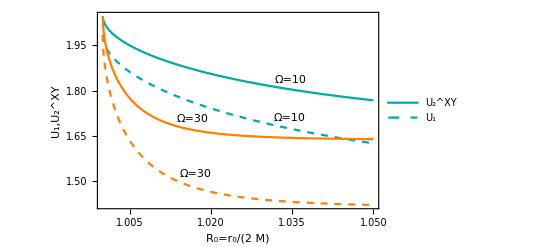

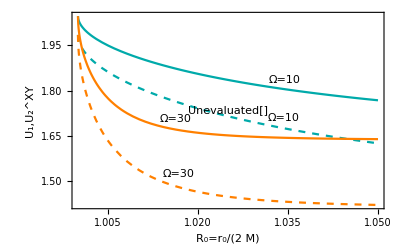

```mathematica
(*----------------Subscript[U, 2]^xy-----------------*)
Clear[q2XY,u1,o,r];
u1[o_,r_]:=Log[2,8/3]+sAR[o,r]-sR[o,r]; 
q2XY[o_,r_] = Simplify[Log[2,8/3]+sA[o,r]-2 *sR[o,r] + sX[o,r] + sY[o,r]];
q2XY[50,1.00]
q2XY[30,1.05] 
Plot[{q2XY[10,r],u1[10,r],q2XY[30,r],u1[30,r]}, {r,1,1.05},Frame->True,FrameLabel -> {"R_0=r_0/(2  M)","U_1,U_2^XY"},PlotStyle->{{Darker[Cyan]},{Darker[Cyan],Dashed},{Orange},{Orange,Dashed},{Dashed,Thickness[0.001]},{Dashed,Thickness[0.001]}},RotateLabel->False,PlotLegends->Placed[{"U_2^XY","U_1"},Center],PlotLabels->Placed[{"Ω=10","Ω=10","Ω=30","Ω=30"},{Scaled[0.85],Above}]]
```

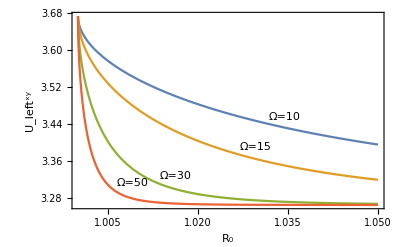

```mathematica
(*----------------left-----------------*)
Clear[left,o,r];
left[o_,r_]:= sXR[o,r]+sYR[o,r]-2 sR[o,r];
Plot[{left[10,r],left[15,r],left[30,r],left[50,r]}, {r,1,1.05},Frame->True,FrameLabel -> {"R_0","U_left^xy"},RotateLabel->False,PlotLabels->Placed[{"Ω=10","Ω=15","Ω=30","Ω=50"},{Scaled[0.85],Above}]]
```

```mathematica
left[50,1.00]
left[50,1.5]
```

3.67323

3.26396

```mathematica
(*----------------difxy-----------------*)
Clear[dif,difu1,o,r];
difu1[o_,r_]:= left[o,r]-u1[o,r];
dif[o_,r_]:= left[o,r]-q2XY[o,r];
Plot[{dif[10,r],difu1[10,r],dif[30,r],difu1[30,r]}, {r,1,1.05},Frame->True,RotateLabel->False,FrameLabel -> {"R_0=r_0/(2  M)","Δ_1,Δ_2^XY"},PlotStyle->{{Darker[Cyan]},{Darker[Cyan],Dashed},{Darker[Cyan]},{Orange,Dashed},{Dashed,Thickness[0.001]}},RotateLabel->False,PlotLegends->Placed[{"Δ_2^XY","Δ_1"},Center],PlotLabels->Placed[{"Ω=10","Ω=10","Ω=30","Ω=30"},{Scaled[0.85],Above}]]
```

```mathematica
(*----------------Subscript[U, 2]^xz-----------------*)
Clear[q2XZ,o,r];
q2XZ[o_,r_] = Simplify[Log[2,8/3]+sA[o,r]-2 *sR[o,r] + sX[o,r] + sZ[o,r]];
q2XZ[50,1.00]
q2XZ[50,1.5] 
Plot[{q2XZ[10,r],q2XZ[15,r],q2XZ[30,r],q2XZ[50,r]}, {r,1,1.05},Frame->True,FrameLabel -> {"R_0","U_2^xy"},RotateLabel->False,PlotStyle->{{},{},{},{},{Dashed}},PlotLabels->Placed[{"Ω=10","Ω=15","Ω=30","Ω=50"},{Scaled[0.85],Above}]]
```

1.81264

1.73382

$Aborted

```mathematica
sXR[50,1.00]
sXR[50,1.05]
sZR[50,1.00]
sZR[50,1.05]
sR[50,1.00]
sR[50,1.05]
```

3.75491

2.55062

2.79248

1.58538

1.9183

0.918622

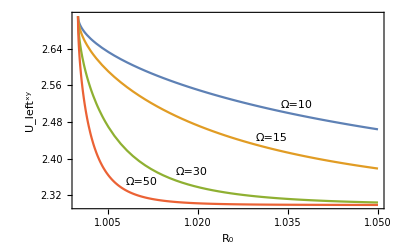

```mathematica
(*----------------leftxz-----------------*)
Clear[left,o,r];
left[o_,r_]:= sXR[o,r]+sZR[o,r]-2 sR[o,r];
Plot[{left[10,r],left[15,r],left[30,r],left[50,r]}, {r,1,1.05},Frame->True,FrameLabel -> {"R_0","U_left^xy"},RotateLabel->False,PlotLabels->Placed[{"Ω=10","Ω=15","Ω=30","Ω=50"},{Scaled[0.85],Above}]]
```

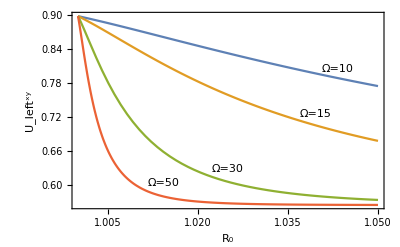

```mathematica
(*----------------difxz-----------------*)
Clear[dif,o,r];
dif[o_,r_]:= left[o,r]-q2XZ[o,r];
Plot[{dif[10,r],dif[15,r],dif[30,r],dif[50,r]}, {r,1,1.05},Frame->True,FrameLabel -> {"R_0","U_left^xy"},RotateLabel->False,PlotLabels->Placed[{"Ω=10","Ω=15","Ω=30","Ω=50"},{Scaled[0.85],Above}]]
```

1.81264

1.73382

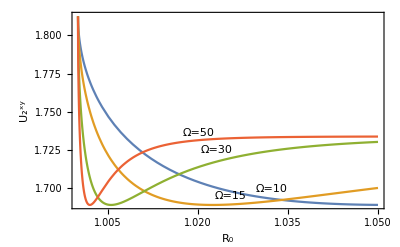

```mathematica
(*----------------Subscript[U, 2]^yz-----------------*)
Clear[q2YZ,o,r];
q2YZ[o_,r_] = Simplify[Log[2,8/3]+sA[o,r]-2 *sR[o,r] + sY[o,r] + sZ[o,r]];
q2YZ[50,1.00]
q2YZ[50,1.5] 
Plot[{q2YZ[10,r],q2YZ[15,r],q2YZ[30,r],q2YZ[50,r]}, {r,1,1.05},Frame->True,FrameLabel -> {"R_0","U_2^xy"},RotateLabel->False,PlotStyle->{{},{},{},{},{Dashed}},PlotLabels->Placed[{"Ω=10","Ω=15","Ω=30","Ω=50"},{Scaled[0.85],Above}]]
```

```mathematica
(*----------------leftyz-----------------*)
Clear[left,o,r];
left[o_,r_]:= sYR[o,r]+sZR[o,r]-2 sR[o,r];
Plot[{left[10,r],left[15,r],left[30,r],left[50,r]}, {r,1,1.05},Frame->True,FrameLabel -> {"R_0","U_left^xy"},RotateLabel->False,PlotLabels->Placed[{"Ω=10","Ω=15","Ω=30","Ω=50"},{Scaled[0.85],Above}]]
```

-Graphics-

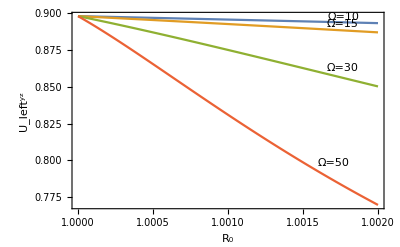

```mathematica
(*----------------difyz-----------------*)
Clear[dif,o,r];
dif[o_,r_]:= left[o,r]-q2YZ[o,r];
Plot[{dif[10,r],dif[15,r],dif[30,r],dif[50,r]}, {r,1,1.002},Frame->True,FrameLabel -> {"R_0","U_left^yz"},RotateLabel->False,PlotLabels->Placed[{"Ω=10","Ω=15","Ω=30","Ω=50"},{Scaled[0.85],Above}]]
```

1.98476

1.41519

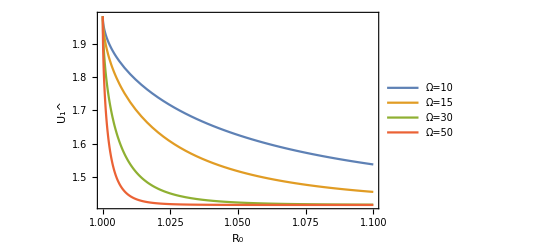

```mathematica
(*----------------Subscript[U, 1]-----------------*)
Clear[u1];
u1[o_,r_]:=Log[2,8/3]+sAR[o,r]-sR[o,r]; 
N[u1[50,1]]
u1[50,1.05]
Plot[{u1[10,r],u1[15,r],u1[30,r],u1[50,r]}, {r,1,1.1},Frame->True,FrameLabel -> {"R_0","U_1^"},RotateLabel->False,PlotStyle->{{},{},{},{},{Dashed}},PlotRange->All,PlotLegends->Placed[{"Ω=10","Ω=15","Ω=30","Ω=50"},{Right,Center}]]
```

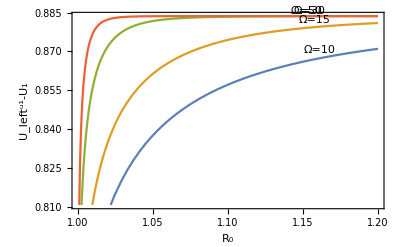

```mathematica
(*----------------difu1-----------------*)
Clear[dif,o,r];
dif[o_,r_]:= left[o,r]-u1[o,r];
Plot[{dif[10,r],dif[15,r],dif[30,r],dif[50,r]}, {r,1,1.2},Frame->True,FrameLabel -> {"R_0","U_left^u1-U_1"},RotateLabel->False,PlotLabels->Placed[{"Ω=10","Ω=15","Ω=30","Ω=50"},{Scaled[0.85],Above}]]
```

```mathematica
"minimum R_0"
{1.2677542082814874,{l1[o,r]->0.2806413659072262}}
```

minimum R_0

{1.26775,{ⅇ^(-o √(1-1/r))→0.280641}}

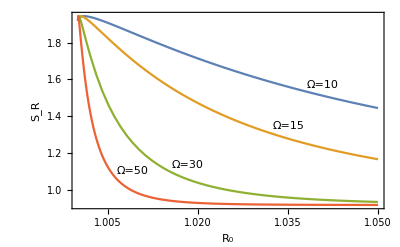

```mathematica
(*----------------R-----------------*)
Plot[{sR[10,r],sR[15,r],sR[30,r],sR[50,r]}, {r,1,1.05},Frame->True,FrameLabel -> {"R_0","S_R"},RotateLabel->False,PlotLabels->Placed[{"Ω=10","Ω=15","Ω=30","Ω=50"},{Scaled[0.85],Above}]]
```

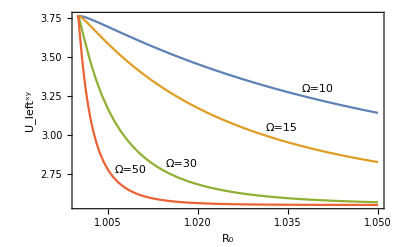

```mathematica
(*----------------XR-----------------*)
Plot[{sXR[10,r],sXR[15,r],sXR[30,r],sXR[50,r]}, {r,1,1.05},Frame->True,FrameLabel -> {"R_0","U_left^xy"},RotateLabel->False,PlotLabels->Placed[{"Ω=10","Ω=15","Ω=30","Ω=50"},{Scaled[0.85],Above}]]
```

```mathematica
(*----------------YR-----------------*)
Plot[{sYR[10,r],sYR[15,r],sYR[30,r],sYR[50,r]}, {r,1,1.05},Frame->True,FrameLabel -> {"R_0","U_left^xy"},RotateLabel->False,PlotLabels->Placed[{"Ω=10","Ω=15","Ω=30","Ω=50"},{Scaled[0.85],Above}]]
```

-Graphics-

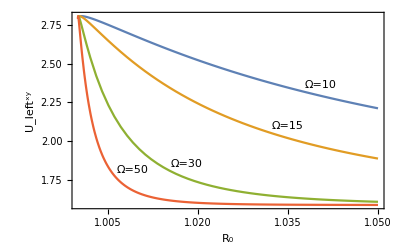

```mathematica
(*----------------ZR-----------------*)
Plot[{sZR[10,r],sZR[15,r],sZR[30,r],sZR[50,r]}, {r,1,1.05},Frame->True,FrameLabel -> {"R_0","U_left^xy"},RotateLabel->False,PlotLabels->Placed[{"Ω=10","Ω=15","Ω=30","Ω=50"},{Scaled[0.85],Above}]]
```

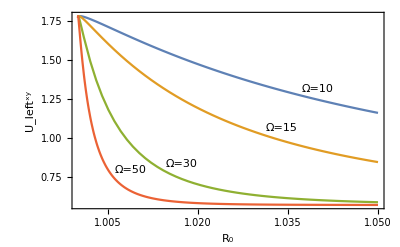

```mathematica
(*----------------X-----------------*)
Plot[{sX[10,r],sX[15,r],sX[30,r],sX[50,r]}, {r,1,1.05},Frame->True,FrameLabel -> {"R_0","U_left^xy"},RotateLabel->False,PlotLabels->Placed[{"Ω=10","Ω=15","Ω=30","Ω=50"},{Scaled[0.85],Above}]]
```

```mathematica
(*----------------Y-----------------*)
Plot[{sY[10,r],sY[15,r],sY[30,r],sY[50,r]}, {r,1,1.05},Frame->True,FrameLabel -> {"R_0","U_left^xy"},RotateLabel->False,PlotLabels->Placed[{"Ω=10","Ω=15","Ω=30","Ω=50"},{Scaled[0.85],Above}]]
```

-Graphics-

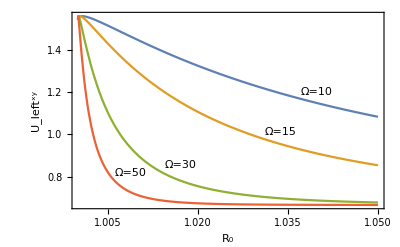

```mathematica
(*----------------Z-----------------*)
Plot[{sZ[10,r],sZ[15,r],sZ[30,r],sZ[50,r]}, {r,1,1.05},Frame->True,FrameLabel -> {"R_0","U_left^xy"},RotateLabel->False,PlotLabels->Placed[{"Ω=10","Ω=15","Ω=30","Ω=50"},{Scaled[0.85],Above}]]
```

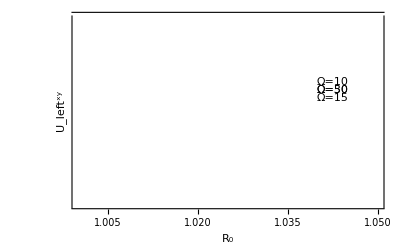

```mathematica
(*----------------XR-X-----------------*)
Plot[{sXR[10,r]-sX[10,r],sXR[15,r]-sX[15,r],sXR[30,r]-sX[30,r],sXR[50,r]-sX[50,r]}, {r,1,1.05},Frame->True,FrameLabel -> {"R_0","U_left^xy"},RotateLabel->False,PlotLabels->Placed[{"Ω=10","Ω=15","Ω=30","Ω=50"},{Scaled[0.85],Above}]]
```

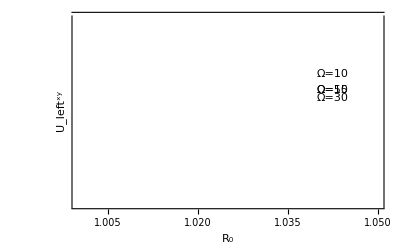

```mathematica
(*----------------YR-Y-----------------*)
Plot[{sYR[10,r]-sY[10,r],sYR[15,r]-sY[15,r],sYR[30,r]-sY[30,r],sYR[50,r]-sY[50,r]}, {r,1,1.05},Frame->True,FrameLabel -> {"R_0","U_left^xy"},RotateLabel->False,PlotLabels->Placed[{"Ω=10","Ω=15","Ω=30","Ω=50"},{Scaled[0.85],Above}]]
```

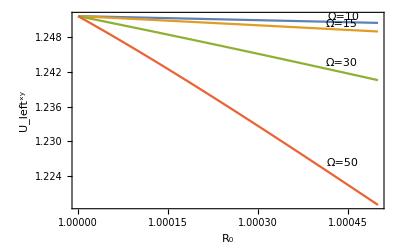

```mathematica
(*----------------ZR-Z-----------------*)
Plot[{sZR[10,r]-sZ[10,r],sZR[15,r]-sZ[15,r],sZR[30,r]-sZ[30,r],sZR[50,r]-sZ[50,r]}, {r,1,1.0005},Frame->True,FrameLabel -> {"R_0","U_left^xy"},RotateLabel->False,PlotLabels->Placed[{"Ω=10","Ω=15","Ω=30","Ω=50"},{Scaled[0.85],Above}]]
```

1.3976

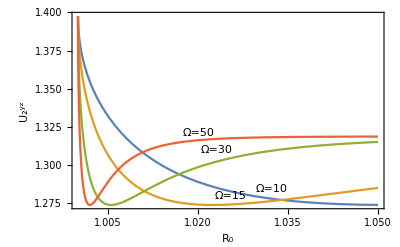

```mathematica
(*----------------Subscript[R, 2]^yz-----------------*)
Clear[q2YZ,g2];
q2YZ[o_,r_] = Simplify[1+sA[o,r]-2 *sR[o,r] + sY[o,r] + sZ[o,r]];
q2YZ[50,1.00]
g2 = Plot[{q2YZ[10,r],q2YZ[15,r],q2YZ[30,r],q2YZ[50,r]}, {r,1,1.05},Frame->True,FrameLabel -> {"R_0","U_2^yz"},RotateLabel->False,PlotStyle->{{},{},{},{},{Dashed}},PlotLabels->Placed[{"Ω=10","Ω=15","Ω=30","Ω=50"},{Scaled[0.85],Above}]]
```

1.4793

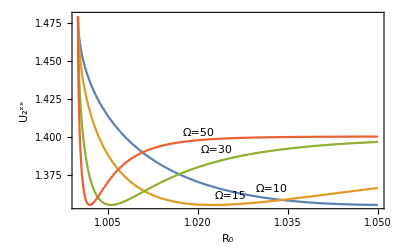

```mathematica
(*----------------Subscript[R, 2]^zx-----------------*)
Clear[q2ZX,g3];
q2ZX[o_,r_] = Simplify[2-2 *sR[o,r] + sZ[o,r] + sX[o,r]];
q2ZX[50,1.00]
g3 = Plot[{q2ZX[10,r],q2ZX[15,r],q2ZX[30,r],q2ZX[50,r]}, {r,1,1.05},Frame->True,FrameLabel -> {"R_0","U_2^zx"},RotateLabel->False,PlotStyle->{{},{},{},{},{Dashed}},PlotLabels->Placed[{"Ω=10","Ω=15","Ω=30","Ω=50"},{Scaled[0.85],Above}]]
```